```mathematica
u1[z1_, q_] = Sqrt[q]*z1
u2[z1_, z2_, cPrev_, q_] = Sqrt[q]*(cPrev*z1 + Sqrt[1 - cPrev^2]*z2)
```

√q z1

√q (cPrev z1+√(1-cPrev^2) z2)

```mathematica
phi[x_] = Tanh[x]
```

Tanh[x]

```mathematica
normalDistr[z_] = (1/Sqrt[2*Pi])*E^((-z^2)/2)
```

(ⅇ^(-z^2/2))/(√(2 π))

```mathematica
qAAStar = 10
```

10

```mathematica
qAB[paRsigmaW_, paRsigmaB_, paRcPrev_, paRqAAStar_] = paRsigmaW^2 * NIntegrate[NIntegrate[phi[u1[z1, paRqAAStar]]*phi[u2[z1, z2, paRcPrev, paRqAAStar]]*normalDistr[z1] * normalDistr[z2], {z1,-15, 15}], {z2,-15, 15}] +paRsigmaB^2
```

paRsigmaB^2+paRsigmaW^2 NIntegrate[NIntegrate[phi[u1[z1,paRqAAStar]] phi[u2[z1,z2,paRcPrev,paRqAAStar]] normalDistr[z1] normalDistr[z2],{z1,-15,15}],{z2,-15,15}]

NIntegrate::ilim: Invalid integration variable or limit(s) in z2.

paRsigmaB+paRsigmaW NIntegrate[NIntegrate[phi[u1[z1,paRqAAStar]] phi[u2[z1,z2,paRcPrev,paRqAAStar]] normalDistr[z1] normalDistr[z2],z1],z2]

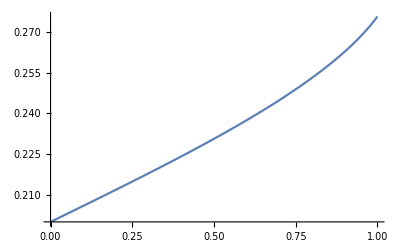

```mathematica
Plot[qAB[1, 2, c, 10]/10, {c, 0, 1}]
```

```mathematica
qAA[qAAPrev_, paRsigmaW_, paRsigmaB_] = paRsigmaW^2 * NIntegrate[(phi[Sqrt[qAAPrev]*z1]^2)*normalDistr[z1], {z1,-15,15}] + paRsigmaB^2
```

paRsigmaB^2+paRsigmaW^2 NIntegrate[phi[√qAAPrev z1]^2 normalDistr[z1],{z1,-15,15}]

```mathematica
sigmaB = 2
sigmaW = 3
```

2

3

0.3

4

1

12.6041

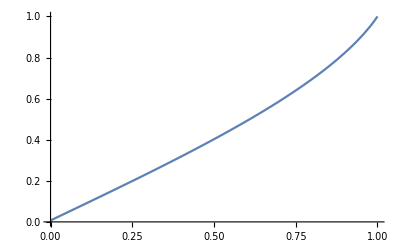

```mathematica
sigmaB = 0.3
sigmaW = 4
qAAPrev = 1
Do[qAAPrev = qAA[qAAPrev, sigmaW, sigmaB], 20]
qAAStar = qAAPrev
p1 = Plot[qAB[sigmaW, sigmaB, c, qAAStar]/qAAStar, {c, 0, 1}]
```

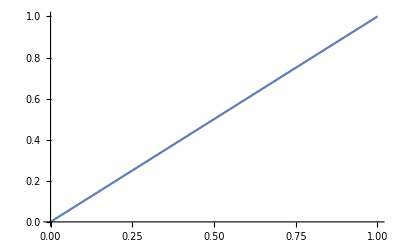

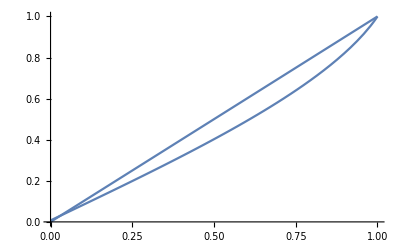

```mathematica
p2 = Plot[c, {c, 0, 1}]
Show[p1, p2]
```

```mathematica
sigmaB = 0.3
sigmaW = 4
qAAPrev = 1
Do[qAAPrev = qAA[qAAPrev, sigmaW, sigmaB], 20]
qAAStar = qAAPrev
```

0.3

4

1

12.6041

```mathematica
NIntegrate[((qAB[sigmaW, sigmaB, c, qAAStar]/qAAStar) - c)^2, {c, 0, 1}]
```

0.00634368

```mathematica
Plot3D[NIntegrate[((qAB[sigmaW, sigmaB, c, qAAStar]/qAAStar) - c)^2, {c, 0, 1}],{sigmaW,0,4},{sigmaB,0,4},PlotPoints->2,Mesh->All,MaxRecursion->0]
```

-Graphics3D-